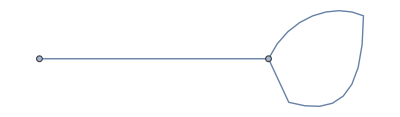

```mathematica
(* Matches (46) of paper *)
G =Graph[{1 <->1, 1 <->2}]
```



```mathematica
(* Matches (57) of paper*)
G=Graph[{1 <->2, 1 <->3, 1 <->4}]
```

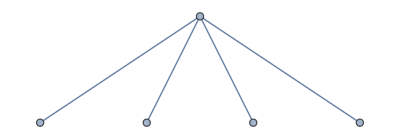

```mathematica
G=Graph[{1 <->2, 1 <->3, 1 <->4, 1 <->5}]
```

```mathematica
G = Graph[{1 <->2, 1<->2}]
```

-Graphics-

```mathematica
G = Graph[{1 <->2, 1<->2, 2<->3, 1<->3}]
```

-Graphics-

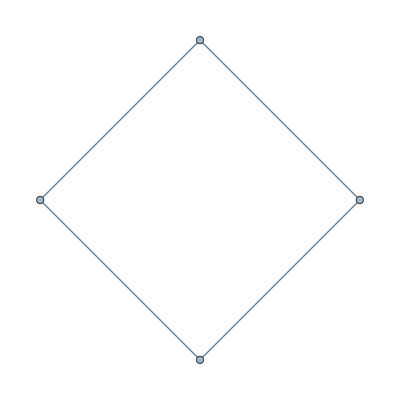

```mathematica
G = Graph[{1 <->2, 2 <->3, 3<->4, 4<->1}]
```

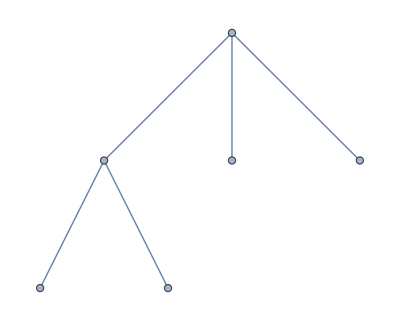

```mathematica
G = Graph[{1 <->2, 1 <->3, 1<->4, 2<->5, 2<->6}]
```

```mathematica
G = Graph[{1 <->2, 1 <->2, 1<->2, 1<->2}]
```

-Graphics-

```mathematica
G = Graph[{1 <->2, 1 <->2, 2<->4, 1<->3}]
```

-Graphics-

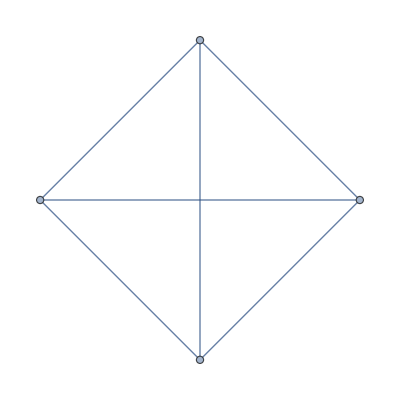

```mathematica
G =Graph[{1 <->2, 1 <->3, 3<->2, 1<->4, 2<->4, 3<->4}]
```

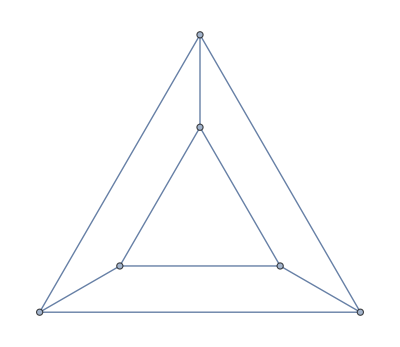

```mathematica
G = PetersenGraph[3,1]
```

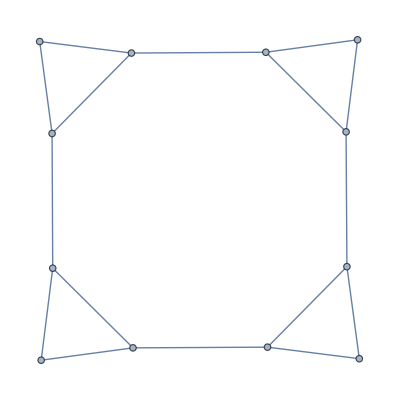

```mathematica
G = Graph[{1 <->2, 1 <->3, 2<->3,2 <->4, 3 <->5, 4<->6,4 <->7, 5 <->8, 5<->9, 6 <->7, 7 <->10, 8<->9, 9 <->11, 10<->11,10 <->12, 11 <->12}]
```

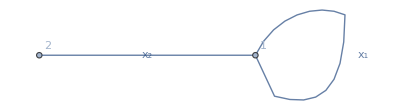

(2/3 | 0 | -1/3 | 2/3
2/3 | 0 | 2/3 | -1/3
-1/3 | 0 | 2/3 | 2/3
0 | 1 | 0 | 0)

```mathematica
(* The below code will output the bond scattering matrix for the above compiled graph *)
V = VertexList[G];
Es= EdgeList[G];
De[i_] := Which[2∣i, Reverse[Es[[i/2]]],!2∣i, Es[[(i + 1)/2]]]
dv[j_] := VertexDegree[G, De[j][[2]]]

sign[i_,j_]:=Which[
Ceiling[i/2]==Ceiling[j/2] && i  ≠ j,  2/ dv[j]  - 1,
De[i][[1]] == De[j][[2]] ,  2/ dv[j] ,
True, 0]

M = Table[sign[i,j], {i,2 Length[Es]},{j,2 Length[Es]}];
(* This formats the matrix where each odd numbered cols/rows is proceeded by the col/row corresponding to opposite oriented edge copy. As in (46) of paper.*)
M//MatrixForm;

reversed=Table[2*x, {x,Range[Length[Es]]}];
edges = Table[2*x-1, {x,Range[Length[Es]]}];
ord = Join[edges,reversed];
(* This formats the matrix where first |E| cols/rows corespond to edges in one orientation and last |E| cols/rows correspond to edges copies in opposite orientation. As in (57) of paper*)
S = M[[ord,ord]];
Show[SetProperty[SetProperty[G,EdgeLabels->Table[Es[[i]] -> Subscript[x, i], {i,1,Length[Es]}]],VertexLabels->"Name"]]
S // MatrixForm
```

```mathematica
(* Outputs Secular determinant *)
(*Di= DiagonalMatrix[Join[Table[Subscript[x, i], {i,Range[Length[Es]]}],Table[Subscript[x, i], {i,Range[Length[Es]]}]]];*)
Di= DiagonalMatrix[Table[Subscript[x, i], {i,Range[2*Length[Es]]}]];
IdentityMatrix[2*Length[Es]] - S. Di // MatrixForm
(* pe is the resulting polynomial of not identifying both copies of edges *)
pe= Expand[Det[IdentityMatrix[2*Length[Es]] - S. Di]];
p = pe /. Table[Subscript[x, i + Length[Es]]-> Subscript[x, i],{i,1,Length[Es]}];
p
(* p is the secular determinant*)
```

(1-(2 x_1)/3 | 0 | x_3/3 | -(2 x_4)/3
-(2 x_1)/3 | 1 | -(2 x_3)/3 | x_4/3
x_1/3 | 0 | 1-(2 x_3)/3 | -(2 x_4)/3
0 | -x_2 | 0 | 1)

1-(4 x_1)/3+x_1^2/3+x_2^2/3-4/3 x_1 x_2^2+x_1^2 x_2^2

```mathematica
(* Here is an example of computing the eigenvalues for the following graph. The zeros of the following function corresponds to eigen values of the Laplacian *)
```

-Graphics-

2/3 (Cos[(√2-π) t]-4 Cos[π t]+3 Cos[(√2+π) t])

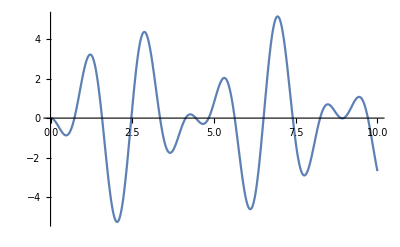

```mathematica
G =Graph[{1 <->1, 1 <->2}]
S = ({{2/3, 0, -1/3, 2/3}, {2/3, 0, 2/3, -1/3}, {-1/3, 0, 2/3, 2/3}, {0, 1, 0, 0}});
P = 1-(4 Subscript[x, 1])/3+Subscript[x, 1]^2/3+Subscript[x, 2]^2/3-4/3 Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 2]^2;
(* normalizing as in Lemma 5.5 of the paper to make Mathematica not complain *)
F = (Exp[-I(Subscript[l, 1]+ Subscript[l, 2])t]/ Sqrt[Det[S]])(P /. Subscript[x, 1]-> Exp[I Subscript[l, 1] t] /. Subscript[x, 2]-> Exp[I Subscript[l, 2] t]);
Fs = FullSimplify[F]
Subscript[l, 1] = Sqrt[2];
Subscript[l, 2] = π;
Plot[Fs, {t,0,10}]
```